```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Генерация второй гармоники в нелинейном кристалле/Книга1.xlsx,/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Генерация второй гармоники в нелинейном кристалле/~$Книга1.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Генерация второй гармоники в нелинейном кристалле/Книга1.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dateset1

```mathematica
dataset1=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"d"->(#d &),"a"-> (Around[#a, #da] &)|>]
```

Dataset[<>]

```mathematica
mydata = raw⟦3⟧⟦3;;⟧⟦All,1;;2⟧
```

{{10.,0.809524},{20.,0.619048},{30.,0.571429},{40.,0.52381},{50.,0.52381},{60.,0.52381},{40.,0.47619},{0.,1.},{-10.,1.},{-20.,0.666667},{-30.,0.47619},{-40.,0.47619}}

```mathematica
mydata1={{10.,0.8095238095238095},{20.,0.6190476190476191},{30.,0.5714285714285714},{50.,0.5238095238095238},{60.,0.5238095238095238},{40.,0.47619047619047616},{0.,1.},{-10.,1.},{-20.,0.6666666666666666},{-30.,0.47619047619047616},{-40.,0.47619047619047616}}
```

{{10.,0.809524},{20.,0.619048},{30.,0.571429},{50.,0.52381},{60.,0.52381},{40.,0.47619},{0.,1.},{-10.,1.},{-20.,0.666667},{-30.,0.47619},{-40.,0.47619}}

```mathematica
func =Interpolation[mydata1]
```

InterpolatingFunction[…]

```mathematica
Plot[func,{x,0,1}]
```

-Graphics-

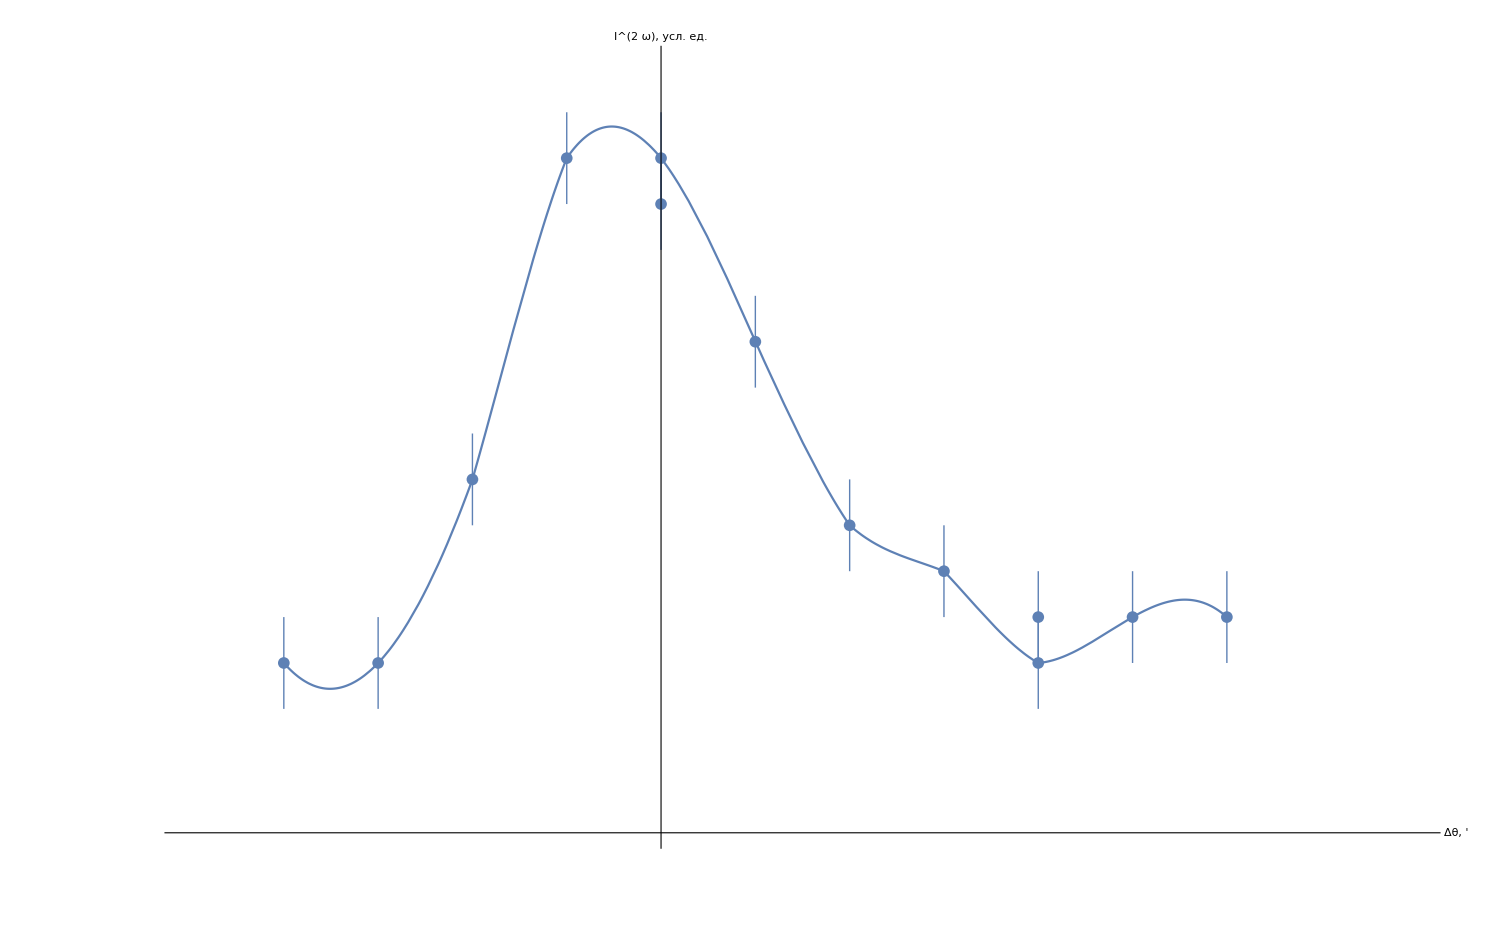

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
Ticks-> {Range[-1000,1000,5],Range[-10,1000,0.1]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["Δθ, '",Large],Style["I^(2  ω), усл. ед.",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{-50,80},{0.3,1.1}},

GridLines->{Range[-1000,1000,2], Range[-10,1000,0.025]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"L_1 = 91,5 см","L_2 = 46 см"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.75]}
]
],
Plot[func[x],{x,-40,60}]
(*,
Plot[
{line1@x,line2@x},
{x,-4, 7},
PlotLegends->Placed[
LineLegend[
{Normal@line1, Normal@line2},
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.4],Scaled[0.75]}
]
]*)
]
```